## CellVertexNumbers-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 14:35:27
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

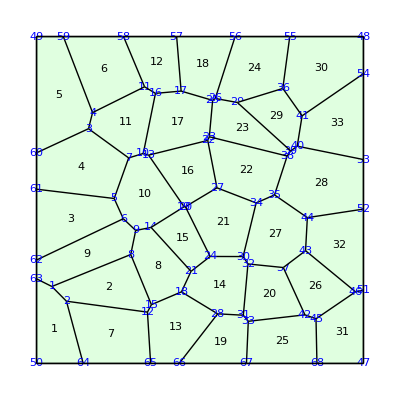

```mathematica
w=TemplateRandomSquareGrid[36, {-5,-5}, {5, 5}];
ShowTissue[w, "CellNumbers"-> True, "VertexNumbers"-> Directive[Blue, FontFamily-> "Verdana"]]
```

Determine the vertex numbers for cell 15

```mathematica
CellVertexNumbers[w,15]
```

{14,21,24,20,19}

Determine the edge numbers for cell 15

```mathematica
c15=TissueCells[w][[15]]
```

{29,39,37,36,28}

Determine the edge numbers for cell 23

```mathematica
c23=TissueCells[w][[23]]
```

{42,43,67,52,46,45}

Find the list of all edges

```mathematica
e=TissueEdges[w]
```

{{1,2},{1,8},{1,63},{2,12},{2,64},{3,4},{3,7},{3,60},{4,11},{4,59},{5,6},{5,7},{5,61},{6,9},{6,62},{7,10},{8,9},{8,15},{9,14},{10,13},{10,16},{11,16},{11,58},{12,15},{12,65},{13,19},{13,22},{14,19},{14,21},{15,18},{16,17},{17,25},{17,57},{18,21},{18,28},{19,20},{20,24},{20,27},{21,24},{22,23},{22,27},{23,25},{23,38},{24,30},{25,26},{26,29},{26,56},{27,34},{28,31},{28,66},{29,36},{29,39},{30,32},{30,34},{31,32},{31,33},{32,37},{33,42},{33,67},{34,35},{35,38},{35,44},{36,41},{36,55},{37,42},{37,43},{38,39},{39,40},{40,41},{40,53},{41,54},{42,45},{43,44},{43,46},{44,52},{45,46},{45,68},{46,51},{47,51},{47,68},{48,54},{48,55},{49,59},{49,60},{50,63},{50,64},{51,52},{52,53},{53,54},{55,56},{56,57},{57,58},{58,59},{60,61},{61,62},{62,63},{64,65},{65,66},{66,67},{67,68}}

Find the vertex numbers for cell 15

```mathematica
CellVertexNumbers[c15, e]
```

{14,21,24,20,19}

Find the vertex numbers for cells 15 and 23

```mathematica
CellVertexNumbers[{c15,c23}, e]
```

{{14,21,24,20,19},{23,25,26,29,39,38}}

Find the list of vertex numbers for every cell in the tissue

```mathematica
CellVertexNumbers[w]
```

{{50,64,2,1,63},{1,2,12,15,8},{61,62,6,5},{60,61,5,7,3},{49,60,3,4,59},{58,59,4,11},{64,65,12,2},{8,15,18,21,14,9},{62,63,1,8,9,6},{5,7,10,13,19,14,9,6},{3,4,11,16,10,7},{57,58,11,16,17},{65,66,28,18,15,12},{18,21,24,30,32,31,28},{14,21,24,20,19},{13,19,20,27,22},{10,16,17,25,23,22,13},{56,57,17,25,26},{66,67,33,31,28},{31,33,42,37,32},{20,24,30,34,27},{22,27,34,35,38,23},{23,25,26,29,39,38},{55,56,26,29,36},{67,68,45,42,33},{37,42,45,46,43},{30,34,35,44,43,37,32},{52,53,40,39,38,35,44},{29,39,40,41,36},{48,55,36,41,54},{46,51,47,68,45},{51,52,44,43,46},{53,54,41,40}}